# Report Project 3

Course code: IX1500
Date: 2018-10-24

Rikard Jakobsson, rikjak@kth.se

Task 1: Dijkstra

## Summary

### Task

a) Explain how Dijkstra’s algorithm works. Use Mathematica graph-methods to illustrate your explanation with an animation.

### Result

Dijskstra’s algorithm finds the shortest path between two vertices in a graph by using a version of a breath first search. You start by marking the distance to all nodes directly reachable from the start node in a list, and setting the rest to infinity. You then add the reachable ones to a priority queue. For each element in the priority queue you check its adjacent nodes. If the distance to one of these is bigger than the current distance plus the distance there from the current node you update it and add the current node as the ‘parent’ to the node looked at. When this is done you can recursively get the shortest path to a node from the start node.

## Code

(1 | 2 | 3 | 6 | 4 | 5 | 7 | 8 | 9
0 | 8 | 4 | 7 | 11 | 13 | 14 | 16 | ∞
0 | 1 | 1 | 1 | 2 | 5 | 3 | 6 | 0)

(0 | 8 | 4 | 7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 10 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

1

5

{1,{1},{0,∞,∞,∞,∞,∞,∞,∞,∞},2,{2,3,4},{0,8,4,7,∞,∞,∞,∞,∞},3,{3,4,5,6},{0,8,4,7,11,18,∞,∞,∞},6,{4,5,6,7},{0,8,4,7,11,18,14,∞,∞},4,{5,6,7},{0,8,4,7,11,18,14,∞,∞},5,{6,7,6},{0,8,4,7,11,13,14,∞,∞},7,{7,6,8},{0,8,4,7,11,13,14,16,∞},5,{6,8},{0,8,4,7,11,13,14,16,∞},8,{8,8},{0,8,4,7,11,13,14,16,∞},8,{8},{0,8,4,7,11,13,14,16,∞}}

{1,2,4}

{1,2,4}

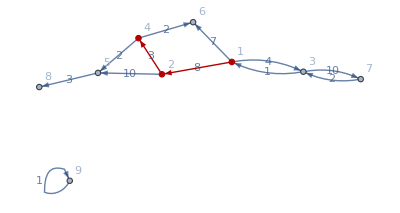

(a | b | c | f | e | d | g | h | i
0 | 8 | 4 | 7 | 11 | 18 | 14 | 14 | ∞
0 | 1 | 1 | 1 | 2 | 2 | 3 | 5 | 0)

(0 | 8 | 4 | 7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 10 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{1,{1},{0,∞,∞,∞,∞,∞,∞,∞,∞},2,{2,3,4},{0,8,4,7,∞,∞,∞,∞,∞},3,{3,4,5,6},{0,8,4,7,11,18,∞,∞,∞},6,{4,5,6,7},{0,8,4,7,11,18,14,∞,∞},4,{5,6,7},{0,8,4,7,11,18,14,∞,∞},5,{6,7,6},{0,8,4,7,11,13,14,∞,∞},7,{7,6,8},{0,8,4,7,11,13,14,16,∞},5,{6,8},{0,8,4,7,11,13,14,16,∞},8,{8,8},{0,8,4,7,11,13,14,16,∞},8,{8},{0,8,4,7,11,13,14,16,∞},a,{1},{0,∞,∞,∞,∞,∞,∞,∞,∞},b,{2,3,4},{0,8,4,7,∞,∞,∞,∞,∞},c,{3,4,5,6},{0,8,4,7,11,18,∞,∞,∞},f,{4,5,6,7},{0,8,4,7,11,18,14,∞,∞},e,{5,6,7},{0,8,4,7,11,18,14,∞,∞},d,{6,7,8},{0,8,4,7,11,18,14,14,∞},g,{7,8},{0,8,4,7,11,18,14,14,∞},h,{8},{0,8,4,7,11,18,14,14,∞}}

{a,b,d}

{a,b,d}

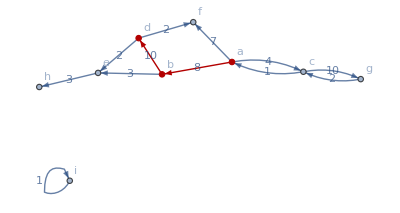

```mathematica
g = Graph[{1->2,1->3,1->6,2->4,2->5,3->7,3->1,4->5,4->6,5->8,7->3,9->9},EdgeWeight->{8,4,7,3,10,10,1,2,2,3,2,1},VertexLabels->Automatic,EdgeLabels->"EdgeWeight"];
g2 = Graph[{"a"->"b","a"->"c","a"->"f","b"->"e","b"->"d","c"->"g","c"->"a","d"->"e","d"->"f","e"->"h","g"->"c","i"->"i"},EdgeWeight->{8,4,7,3,10,10,1,2,2,3,2,1},VertexLabels->Automatic,EdgeLabels->"EdgeWeight"];


distance = {};
parent = {};
test = {};
path ={};
dijkstra[graph_,from_,to_]:= (parent = ConstantArray[0,Length[VertexList[graph]]];
path ={};
queue = {};
visited={};

vl = VertexList[graph];
posFrom = Position[vl,n_/;n==from][[1]][[1]];
posTo = Position[vl,n_/;n==to][[1]][[1]];
distance =ConstantArray[Infinity,Length[VertexList[graph]]];
adjacent =Normal[WeightedAdjacencyMatrix[graph]];
parent[[posFrom]] =0;
distance[[posFrom]] = 0;
addToQueue[posFrom];
While[(Length[queue]>0 ),(
element =queue[[1]];
AppendTo[visited,element];
AppendTo[test,vl[[element]]];
AppendTo[test,queue];
AppendTo[test,distance];
(*AppendTo[test,visited];*)
fillDistance[element];
If[element == posTo,Break];
); queue = Delete[queue,1];
];
(*fillDistance[from,from];*)

addToQueue[node_]:=(AppendTo[queue,node];
Sort[queue,distance[[#1]]<distance[[#2]]&];
);
getFromQueue[]:=(
a  = queue[[1]];
queue =Delete[queue,1];
Return[a]
);
fillDistance[row_]:=(For[i = 1,i<Length[adjacent[[row]]],i++,
If[adjacent[[row]][[i]]≠0,
(If[distance [[i]]>(adjacent[[row]][[i]]+distance[[row]]),
(distance [[i]]=(adjacent[[row]][[i]]+distance[[row]]);
parent[[i]]=row)];
If[(Not[MemberQ[visited,i]]),addToQueue[i]]);

];
]);
p = parent[[posTo]];
AppendTo[path,vl[[posTo]]];
While[p≠posFrom,(AppendTo[path,vl[[p]]]
);p = parent[[p]]];
AppendTo[path,vl[[posFrom]]];
path = Reverse[path];
);

origin = 1;
destination =4;
dijkstra[g,origin,destination];
MatrixForm[{ VertexList[g],distance,parent}]
MatrixForm[adjacent]
posFrom
posTo

test
path
FindShortestPath[g,origin,destination]
HighlightGraph[g,PathGraph[FindShortestPath[g,origin,destination,Method->"Dijkstra"],DirectedEdges->True]]



origin = "a";
destination ="d";
dijkstra[g2,origin,destination];
MatrixForm[{ VertexList[g2],distance,parent}]
MatrixForm[adjacent]
test
path
FindShortestPath[g2,origin,destination]
HighlightGraph[g2,PathGraph[FindShortestPath[g2,origin,destination,Method->"Dijkstra"],DirectedEdges->True]]
```